Run all the sections!

```mathematica
Quit[]
```

## Quick Background Estimate

```mathematica
(*See Set_Limits_milliQ_notes.pdf in README*)
```

```mathematica
DCrate(*dark current*)=700(*Hz*);
TRunMidLum=1.5*10^7(*in seconds, corresponds to 300fb^-1*);
TRunHighLum=3*10^7(*in seconds, corresponds to 3000fb^-1*);
NPMTperEvent=400.;
TimingResolution=15*10^-9(*5ns*);
```

```mathematica
midLumFullBkg=NPMTperEvent*(TRunMidLum*DCrate)(TimingResolution*DCrate)^2;
highLumFullBkg=NPMTperEvent*(TRunHighLum*DCrate)(TimingResolution*DCrate)^2;
```

```mathematica
(*midLum Run*)
Ceiling@Table[Table[ϵ*midLumFullBkg*t,{t,{5,10,50,300}/300}],{ϵ,{0.01,0.49,1}}]
```

{{1,1,1,5},{4,8,38,227},{8,16,78,464}}

```mathematica
(*highLum Run*)
Ceiling@Table[ϵ*highLumFullBkg,{ϵ,{0.01,0.49,1}}]
```

{10,454,927}

## Initialize

```mathematica
(*These are all the limits from various experiments, and cosmological considerations*)
(* Limits from the Intensity Frontier document... *)
colliders={{9.849*10^-7,2.966*10^-4},{1.388*10^-6,2.966*10^-4},{2.624*10^-6,2.966*10^-4},{5.441*10^-6,2.966*10^-4},{1.450*10^-5,2.906*10^-4},{4.464*10^-5,2.906*10^-4},{1.128*10^-4,2.906*10^-4},{1.937*10^-4,2.906*10^-4},{1.937*10^-4,3.998*10^-4},{1.937*10^-4,5.759*10^-4},{2.717*10^-4,5.759*10^-4},{4.478*10^-4,5.893*10^-4},{7.885*10^-4,5.893*10^-4},{9.788*10^-4,5.893*10^-4},{9.788*10^-4,0.001},{0.001,0.001},{0.002,0.001},{0.002,0.002},{0.002,0.003},{0.003,0.003},{0.005,0.003},{0.008,0.003},{0.010,0.003},{0.010,0.006},{0.010,0.010},{0.020,0.010},{0.037,0.010},{0.056,0.010},{0.091,0.010},{0.091,0.014},{0.091,0.021},{0.091,0.029},{0.100,0.0283830935594},{0.109,0.0284885942089},{0.120,0.0286496073272},{0.133,0.0287541301381},{0.146,0.028920580907},{0.157,0.0290241278939},{0.170,0.0293462092952},{0.180,0.0294686273857},{0.194,0.0296378136845},{0.208,0.0299265768173},{0.221,0.0300399733688},{0.231,0.0304302481094},{0.242,0.0306006535878},{0.252,0.030886890423},{0.263,0.0311704988731},{0.272,0.0312281923909},{0.282,0.0315214212878},{0.291,0.031692270351},{0.302,0.0320437201336},{0.316,0.032403703492},{0.328,0.0327047397177},{0.343,0.033250563905},{0.355,0.0337520369756},{0.367,0.0343394816501},{0.377,0.0351624800035},{0.385,0.0360333179155},{0.392,0.037261239915},{0.398,0.0384551687033},{0.402,0.0397592756473},{0.406,0.0416413256273},{0.408,0.044199547509},{0.413,0.0461389206636},{0.417,0.0485139155295},{0.426,0.0503507696068},{0.438,0.0518613536268},{0.453,0.0531187349247},{0.466,0.0545087148995},{0.483,0.0556453052827},{0.496,0.0571139212452},{0.506,0.0587196730236},{0.514,0.0609097693314},{0.520,0.0632455532034},{0.530,0.0632455532034},{0.536,0.0632455532034},{0.540,0.0632455532034},{0.543,0.0632455532034},{0.545,0.0894427191},{0.547,0.0894427191},{0.550,0.0894427191},{0.550,0.0894427191},{0.550,0.0894427191},{0.552,0.109544511501},{0.556,0.109544511501},{0.560,0.109544511501},{0.571,0.109544511501},{0.585,0.126491106407},{0.600,0.126491106407},{0.619,0.126491106407},{0.638,0.141421356237},{0.658,0.141421356237},{0.675,0.141421356237},{0.696,0.141421356237},{0.718,0.141421356237},{0.738,0.141421356237},{0.756,0.141421356237},{0.776,0.141421356237},{0.792,0.141421356237},{0.810,0.141421356237},{0.825,0.141421356237},{0.841,0.141421356237},{0.865,0.154919333848},{0.889,0.154919333848},{0.910,0.154919333848},{0.931,0.154919333848},{0.953,0.154919333848},{0.974,0.154919333848},{0.996,0.154919333848},{1.020,0.154919333848},{1.043,0.154919333848},{1.065,0.154919333848},{1.084,0.154919333848},{1.108,0.167332005307},{1.132,0.167332005307},{1.160,0.167332005307},{1.182,0.167332005307},{1.208,0.167332005307},{1.234,0.167332005307},{1.260,0.167332005307},{1.286,0.167332005307},{1.313,0.1788854382},{1.342,0.1788854382},{1.366,0.1788854382},{1.387,0.1788854382},{1.409,0.1788854382},{1.434,0.18973665961},{1.455,0.18973665961},{1.474,0.18973665961},{1.498,0.2}(*{0.169,0.030},{0.361,0.030},{0.622,0.030},{0.927,0.030},{0.927,0.060},{0.927,0.128},{0.927,0.236}*),{1.785,0.236},{3.092,0.232},{5.334,0.232},{10.834,0.232},{25.547,0.231},{43.548,0.231},{43.548,0.381},{44.065,0.649},{64.413,0.662},{81.445,0.660},{84.501,0.774},{86.643,0.935}};
SLAC={{9.967*10^-5,1.999*10^-5},{1.776*10^-4,2.402*10^-5},{2.743*10^-4,2.687*10^-5},{4.624*10^-4,3.212*10^-5},{7.499*10^-4,3.593*10^-5},{0.001,3.950*10^-5},{0.002,5.043*10^-5},{0.002,6.062*10^-5},{0.003,7.476*10^-5},{0.004,9.142*10^-5},{0.007,1.205*10^-4},{0.011,1.615*10^-4},{0.023,2.565*10^-4},{0.043,3.674*10^-4},{0.068,4.730*10^-4},{0.098,5.987*10^-4},{0.100,0.001},{0.100,0.003},{0.100,0.007},{0.100,0.024},{0.100,0.085},{0.097,0.328},{0.098,0.619},{0.098,1.0}};
LHC={{43.548,1.0},{43.548,0.321},{45.0,.321},{50,0.321},{99.155,0.321},{99.155,0.321},{144.314,0.312},{219.321,0.312},{287.124,0.312},{276.742,0.489},{276.742,0.626},{324.401,0.626},{380.267,0.626},{380.267,0.802},{380.267,1.0}};
CMBNeff={{0.049,2.162*10^-8},{0.093,3.143*10^-8},{0.179,4.702*10^-8},{0.237,6.088*10^-8},{0.295,7.620*10^-8},{0.374,1.192*10^-7},{0.450,2.487*10^-7},{0.503,4.627*10^-7},{0.475,1.248*10^-6},{0.403,2.523*10^-6},{0.389,4.666*10^-6},{0.410,7.370*10^-6},{0.434,1.181*10^-5},{0.475,2.167*10^-5},{0.538,3.411*10^-5},{0.598,5.014*10^-5},{0.648,9.946*10^-5},{0.710,2.205*10^-4},{0.791,5.453*10^-4},{0.834,0.001},{0.913,0.003},{0.947,0.006},{1.036,0.013},{1.075,0.026},{1.138,0.063},{1.192,0.120},{1.217,0.223},{1.217,1.0}};
BBNNeff={{8.303*10^-5,2.128*10^-9},{1.599*10^-4,2.388*10^-9},{4.879*10^-4,3.303*10^-9},{0.001,5.111*10^-9},{0.003,6.892*10^-9},{0.012,1.179*10^-8},{0.026,1.852*10^-8},{0.068,3.289*10^-8},{0.135,5.710*10^-8},{0.213,1.106*10^-7},{0.213,1.557*10^-7},{0.198,2.087*10^-7},{0.147,2.955*10^-7},{0.108,3.815*10^-7},{0.086,4.653*10^-7},{0.078,4.331*10^-7},{0.073,4.762*10^-7},{0.064,4.244*10^-7},{0.061,3.972*10^-7},{0.056,4.244*10^-7},{0.048,3.729*10^-7},{0.036,4.171*10^-7},{0.028,3.644*10^-7},{0.022,4.679*10^-7},{0.019,6.147*10^-7},{0.019,8.220*10^-7},{0.017,1.105*10^-6},{0.017,1.667*10^-6},{0.016,3.880*10^-6},{0.016,7.733*10^-6},{0.016,2.850*10^-5},{0.016,6.985*10^-5},{0.017,1.693*10^-4}};
CMB={{230.010,1.0},{230.010,1.093*10^-4},{336.222,1.252*10^-4},{646.221,1.649*10^-4},{1468.643,2.322*10^-4},{3601.034,3.413*10^-4},{5619.540,4.496*10^-4},{9850.781,6.203*10^-4},{10176.013,0.003},{10011.046,0.238}};
LHCExtended={{45,1.0},{45.0,.231},{50,0.231},{99.155,0.321}};
```

## 100% Sensitivity

This section takes in the data output from noWaveformSensitivities.cc and plots the sensitivity curve.

```mathematica
ExclusionPlotGeant4[data_,title_]:=Block[{myplot},
myplot=ListLogLogPlot[{data⟦1⟧,data⟦2⟧,data⟦3⟧,data⟦4⟧},PlotStyle->{Black,{Dashed,Black},Blue,{Dashed,Blue}},GridLines->Automatic, ImageSize->Medium,Joined->True,PlotRange->{{0.07,130},{0.0005,2}},Frame->True,PlotLegends->Placed[{"95% CL 300fb^-1","3σ 300fb^-1","95% CL 3000fb^-1","3σ 3000fb^-1"},{0.3,0.66}],InterpolationOrder->1,PlotLabel->Style[title,Medium],FrameLabel->{{Style["ϵ=Q/e",Medium],None},{Style["m_mCP(GeV)",Medium],None}}];
Return[myplot]
]
```

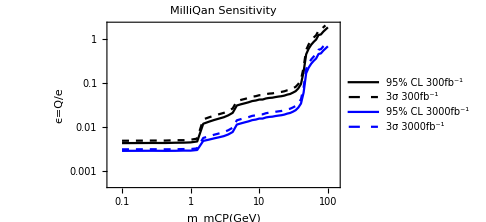

```mathematica
(*Read in exclusion points*)
datG4hundredpc=ToExpression[Import[NotebookDirectory[]<>"noWaveformSensitivities.100pc.dat"]]⟦1,1⟧;
exclusionplots=ExclusionPlotGeant4[datG4hundredpc,"MilliQan Sensitivity"]
```

This section takes in the sensitivity curves plotted above, and superimposes all the various constraints!

```mathematica
EpsLimit45DegTriple10Event={datG4hundredpc⟦1⟧,datG4hundredpc⟦2⟧,datG4hundredpc⟦3⟧,datG4hundredpc⟦4⟧};
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,SLAC];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,LHC];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,CMBNeff];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,colliders];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,BBNNeff];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,CMB];
```

```mathematica
Length[EpsLimit45DegTriple10Event]
```

10

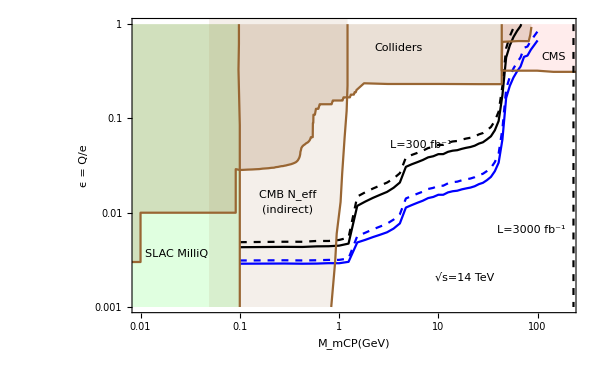

```mathematica
Show[ListLogLogPlot[
Table[EpsLimit45DegTriple10Event[[ii]],{ii,1,Length[EpsLimit45DegTriple10Event]}],Joined->True,PlotStyle-> {Black,{Black,Dashed},Blue,{Blue,Dashed},Brown,Brown,Brown,Brown},PlotRange->{{0.01,200},{0.001,1.0}},Frame->True,FrameLabel->{"M_mCP(GeV)","ϵ = Q/e"},FrameStyle->18,ImageSize->600,Filling->{5->{Top,LightGreen},6->{Top,LightPink},7->{5,Directive[Opacity[0.1],Brown]},8->Top}]
,Epilog->{Inset[Text[Style["CMS",Black,16]],Scaled[{0.95,0.87}]],Inset[Text[Style["CMB N_eff",Black,16]],Scaled[{0.35,0.4}]],
Inset[Text[Style["(indirect)",Black,14]],Scaled[{0.35,0.35}]],Inset[Text[Style["SLAC MilliQ",Black,16]],Scaled[{0.1,0.2}]],
Inset[Text[Style["Colliders",Black,16]],Scaled[{0.6,0.9}]],
Inset[Text[Style["L=300 fb^-1",Black,16]],Scaled[{0.65,0.57}]],
Inset[Text[Style["L=3000 fb^-1",Blue,16]],Scaled[{0.9,0.28}]],
Inset[Text[Style["√s=14 TeV",Black,14]],Scaled[{0.75,0.12}]]}
]
```

```mathematica
(*Change the name as desired*)
Export[NotebookDirectory[]<>"exclusionplot.5b5.assuming150AND300bkg.pdf",%]
```

/Users/chaffy/Work/Repository_MilliCharged/milliq/OfflineAnalysis/Sensitivities/exclusionplot.5b5.assuming150AND300bkg.pdf

## 1 % milliQan

```mathematica
(*Read in exclusion points*)
datG4onepc=ToExpression[Import[NotebookDirectory[]<>"noWaveformSensitivities.1pc.dat"]]⟦1,1⟧;

EpsLimit45DegTriple10Event=Table[datG4onepc⟦2i-1⟧,{i,1,(Length@datG4onepc)/2}];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,datG4hundredpc⟦3⟧];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,SLAC];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,LHC];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,CMBNeff];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,colliders];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,BBNNeff];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,CMB];

Length[EpsLimit45DegTriple10Event]
```

12

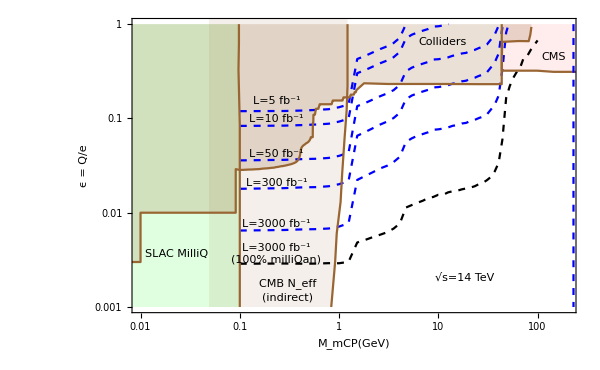

```mathematica
Show[ListLogLogPlot[
Table[EpsLimit45DegTriple10Event⟦ii⟧,{ii,1,Length[EpsLimit45DegTriple10Event]}],Joined->True,
(**)
PlotStyle-> {{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},{Black,Dashed},Brown,Brown,Brown,Brown,Brown},

PlotRange->{{0.01,200},{0.001,1.0}},Frame->True,FrameLabel->{"M_mCP(GeV)","ϵ = Q/e"},FrameStyle->18,ImageSize->600,Filling->{7->{Top,LightGreen},8->{Top,LightPink},9->{7,Directive[Opacity[0.1],Brown]},10->Top}]
,Epilog->{
Inset[Text[Style["CMS",Black,16]],Scaled[{0.95,0.87}]],
Inset[Text[Style["CMB N_eff",Black,16]],Scaled[{0.35,0.1}]],
Inset[Text[Style["(indirect)",Black,14]],Scaled[{0.35,0.05}]],
Inset[Text[Style["SLAC MilliQ",Black,16]],Scaled[{0.1,0.2}]],
Inset[Text[Style["Colliders",Black,16]],Scaled[{0.7,0.92}]],

(**)
Inset[Text[Style["L=5 fb^-1",Black,13]],Scaled[{0.325,0.72}]],
Inset[Text[Style["L=10 fb^-1",Black,13]],Scaled[{0.325,0.66}]],
Inset[Text[Style["L=50 fb^-1",Black,13]],Scaled[{0.325,0.54}]],
Inset[Text[Style["L=300 fb^-1",Black,13]],Scaled[{0.325,0.44}]],
Inset[Text[Style["L=3000 fb^-1",Black,13]],Scaled[{0.325,0.3}]],
Inset[Text[Style["L=3000 fb^-1",Black,13]],Scaled[{0.325,0.22}]],
Inset[Text[Style["(100% milliQan)",Black,13]],Scaled[{0.325,0.18}]],


Inset[Text[Style["√s=14 TeV",Black,16]],Scaled[{0.75,0.12}]]}
]
```

```mathematica
Export["~/Dropbox/Talks/Physics/milliQanSensitivities.2017/Figures/onepcsensitivity.pdf",%]
```

~/Dropbox/Talks/Physics/milliQanSensitivities.2017/Figures/onepcsensitivity.pdf

From 100%milliQan to 1%milliQan, for the 3000fb^-1

```mathematica
√((√B)/S)/.S->(1(*1%*))/(100.(*100%*))/.B->(6(*1%*))/(300.(*1%*))
```

3.7606

```mathematica
datG4onepc⟦9(*lumi/CL*),1(*mass*),2(*d*)⟧/datG4hundredpc⟦3(*lumi/CL*),1(*mass*),2(*d*)⟧
```

2.24846

From 3000fb^-1 to 50fb^-1, 1%milliQan,

```mathematica
√((√B)/S)/.S->50/3000./.B->1/5.
```

5.18004

```mathematica
datG4onepc⟦5(*lumi/CL*),1(*mass*),2(*d*)⟧/datG4onepc⟦9(*lumi/CL*),1(*mass*),2(*d*)⟧
```

5.54652

From 3000fb^-1 to 300fb^-1, 1%milliQan,

```mathematica
√((√B)/S)/.S->300/3000./.B->1/5.
```

2.11474

```mathematica
datG4onepc⟦7(*lumi/CL*),1(*mass*),2(*d*)⟧/datG4onepc⟦9(*lumi/CL*),1(*mass*),2(*d*)⟧
```

2.77111

## 49 % milliQan

```mathematica
(*Read in exclusion points*)
datG4fortyninepc=ToExpression[Import[NotebookDirectory[]<>"noWaveformSensitivities.49pc.dat"]]⟦1,1⟧;

EpsLimit45DegTriple10Event=Table[datG4fortyninepc⟦2i-1⟧,{i,1,(Length@datG4fortyninepc)/2}];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,datG4hundredpc⟦3⟧];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,SLAC];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,LHC];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,CMBNeff];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,colliders];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,BBNNeff];
EpsLimit45DegTriple10Event=Append[EpsLimit45DegTriple10Event,CMB];

Length[EpsLimit45DegTriple10Event]
```

12

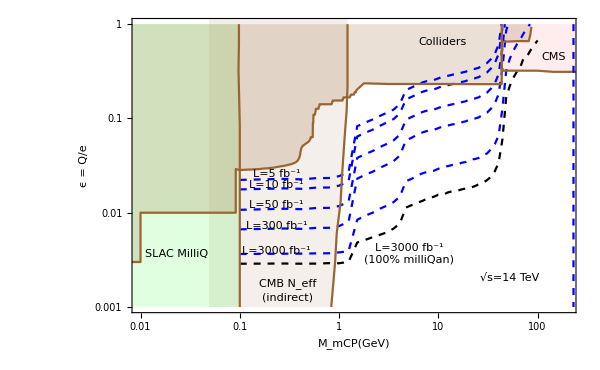

```mathematica
Show[ListLogLogPlot[
Table[EpsLimit45DegTriple10Event⟦ii⟧,{ii,1,Length[EpsLimit45DegTriple10Event]}],Joined->True,
(**)
PlotStyle-> {{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},{Black,Dashed},Brown,Brown,Brown,Brown,Brown},

PlotRange->{{0.01,200},{0.001,1.0}},Frame->True,FrameLabel->{"M_mCP(GeV)","ϵ = Q/e"},FrameStyle->18,ImageSize->600,Filling->{7->{Top,LightGreen},8->{Top,LightPink},9->{7,Directive[Opacity[0.1],Brown]},10->Top}]
,Epilog->{
Inset[Text[Style["CMS",Black,16]],Scaled[{0.95,0.87}]],
Inset[Text[Style["CMB N_eff",Black,16]],Scaled[{0.35,0.1}]],
Inset[Text[Style["(indirect)",Black,14]],Scaled[{0.35,0.05}]],
Inset[Text[Style["SLAC MilliQ",Black,16]],Scaled[{0.1,0.2}]],
Inset[Text[Style["Colliders",Black,16]],Scaled[{0.7,0.92}]],

(**)
Inset[Text[Style["L=5 fb^-1",Black,13]],Scaled[{0.325,0.47}]],
Inset[Text[Style["L=10 fb^-1",Black,13]],Scaled[{0.325,0.433}]],
Inset[Text[Style["L=50 fb^-1",Black,13]],Scaled[{0.325,0.365}]],
Inset[Text[Style["L=300 fb^-1",Black,13]],Scaled[{0.325,0.294}]],
Inset[Text[Style["L=3000 fb^-1",Black,13]],Scaled[{0.325,0.21}]],
Inset[Text[Style["L=3000 fb^-1",Black,13]],Scaled[{0.625,0.22}]],
Inset[Text[Style["(100% milliQan)",Black,13]],Scaled[{0.625,0.18}]],


Inset[Text[Style["√s=14 TeV",Black,16]],Scaled[{0.85,0.12}]]}
]
```

```mathematica
Export["~/Dropbox/Talks/Physics/milliQanSensitivities.2017/Figures/fortyninepcsensitivity.pdf",%]
```

~/Dropbox/Talks/Physics/milliQanSensitivities.2017/Figures/fortyninepcsensitivity.pdf

From 100%milliQan to 49%milliQan, for the 3000fb^-1

```mathematica
√((√B)/S)/.S->(49(*49%*))/(100.(*100%*))/.B->(454(*49%*))/(900.(*100%*))
```

1.20394

```mathematica
datG4fortyninepc⟦9(*lumi/CL*),1(*mass*),2(*d*)⟧/datG4hundredpc⟦3(*lumi/CL*),1(*mass*),2(*d*)⟧
```

1.26852

From 3000fb^-1 to 50fb^-1, 49%milliQan,

```mathematica
√((√B)/S)/.S->50/3000./.B->38/454.
```

4.16637

```mathematica
datG4fortyninepc⟦5(*lumi/CL*),1(*mass*),2(*d*)⟧/datG4fortyninepc⟦9(*lumi/CL*),1(*mass*),2(*d*)⟧
```

2.93925

From 3000fb^-1 to 300fb^-1, 49%milliQan,

```mathematica
√((√B)/S)/.S->300/3000./.B->227/454.
```

2.65915

```mathematica
datG4fortyninepc⟦7+1(*lumi/CL*),1(*mass*),2(*d*)⟧/datG4fortyninepc⟦9+1(*lumi/CL*),1(*mass*),2(*d*)⟧
```

2.03915